```mathematica
Quit;
ClearAll;
```

{{z→InterpolatingFunction[{{0.01, 20.}}, <>],v→InterpolatingFunction[{{0.01, 20.}}, <>]}}

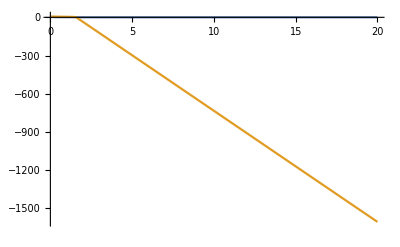

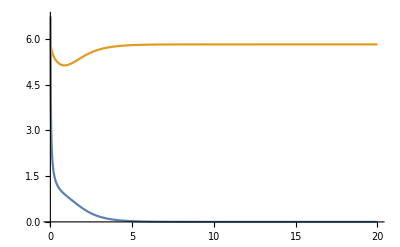

```mathematica
t=6;
m0=1;
a=1/3;
m[v_]:=m0(Tanh[v[x]/a]+1)/2;
zmax=1.1; (*=1/r0*)
Eqn1=1/z[x]^2-v'[x]^2/z[x]^2-v''[x]/z[x]-2/z[x]^2 v'[x]z'[x];
Eqn2=zmax^2/z[x]^4-1/z[x]^2+2/z[x]^2 v'[x]z'[x]+(1/z[x]^2-m[v])v'[x]^2;
x0=0.01;
b=0.;
z0=√(2zmax*x0);
xmax=20;
Sol=NDSolve[{Eqn1==0,Eqn2==0,z[x0]==z0,v[x0]==t-z0+b/2*z0^2, v'[x0]==-zmax/z0+b*zmax},{z,v},{x,x0,xmax}]
Plot[{Evaluate[1/(z[x]/.Sol)],Evaluate[v[x]/.Sol],Evaluate[√m[v[x]]/.Sol]},{x,x0,xmax}]
```